U(V) | 透光率（%）
0.14 | 0.909091
0.74 | 0.909091
1.14 | 1.16883
1.24 | 2.20779
1.29 | 4.09091
1.32 | 5.77922
1.34 | 7.5974
1.44 | 18.3766
1.54 | 34.8701
1.64 | 52.8571
1.74 | 71.2987
1.84 | 76.039
1.89 | 80.
1.92 | 83.7013
1.94 | 85.0649
1.99 | 88.2468
2.04 | 91.039
2.09 | 92.987
2.12 | 94.5455
2.15 | 95.5844
2.17 | 95.7792
2.27 | 98.1818
2.33 | 98.7013
2.35 | 99.7403
2.37 | 99.8052

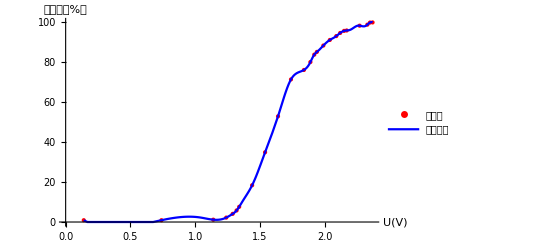

{当 data1 达到 10% 时对应的 data2 值: 1.44,当 data1 达到 90% 时对应的 data2 值: 2.04}

```mathematica
(*定义第一个数据数组*)data1={1.4,1.4,1.8,3.4,6.3,8.9,11.7,28.3,53.7,81.4,109.8,117.1,123.2,128.9,131.0,135.9,140.2,143.2,145.6,147.2,147.5,151.2,152.0,153.6,153.7};

(*理论最大值*)
maxValue=154;

(*将第一个数据数组中的所有数除以最大值并转换为百分数*)
normalizedData1=(data1/maxValue)*100;

(*定义第二个数据数组*)
data2={0.14,0.74,1.14,1.24,1.29,1.32,1.34,1.44,1.54,1.64,1.74,1.84,1.89,1.92,1.94,1.99,2.04,2.09,2.12,2.15,2.17,2.27,2.33,2.35,2.37};

(*找到最接近 10% 和 90% 的索引*)
index10=First@FirstPosition[normalizedData1,_?(#>=10&)];
index90=First@FirstPosition[normalizedData1,_?(#>=90&)];

(*获取对应的 data2 值*)
data2At10Percent=data2[[index10]];
data2At90Percent=data2[[index90]];

(*样条拟合*)
splineFit=Interpolation[Transpose[{data2,normalizedData1}],Method->"Spline",InterpolationOrder->3];

(*确保曲线保持在正值范围*)
positivesplineFit[x_]:=Max[0,splineFit[x]]

(*绘制数据点和样条拟合曲线*)
plot=Show[ListPlot[Transpose[{data2,normalizedData1}],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"U(V)","透光率（%）"},PlotLegends->{"数据点"}],Plot[positivesplineFit[x],{x,Min[data2],Max[data2]},PlotStyle->Blue,PlotLabel->"非负样条拟合曲线",PlotLegends->{"拟合曲线"}]];

(*输出结果表格*)
table=TableForm[Transpose[{data2,normalizedData1}],TableHeadings->{None,{"U(V)","透光率（%）"}}];

table
plot
{"当 data1 达到 10% 时对应的 data2 值: "<>ToString[data2At10Percent],"当 data1 达到 90% 时对应的 data2 值: "<>ToString[data2At90Percent]}
```

```mathematica
=N[2.04/1.44,15]
```

1.41667